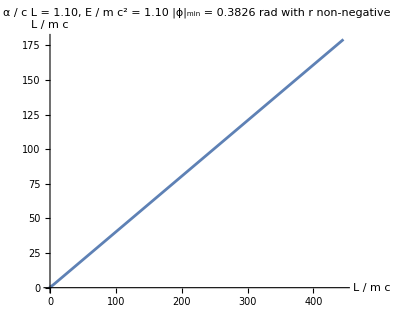

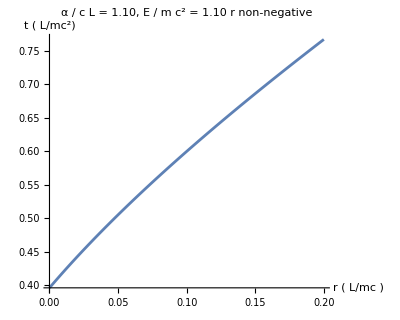

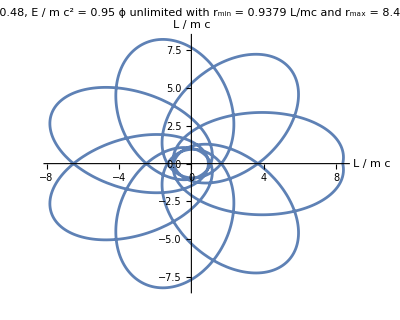

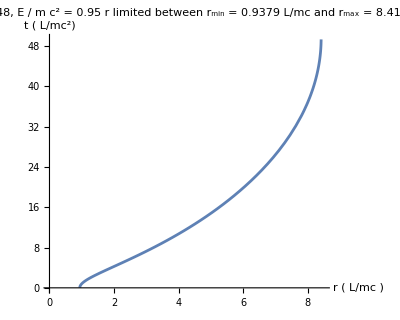

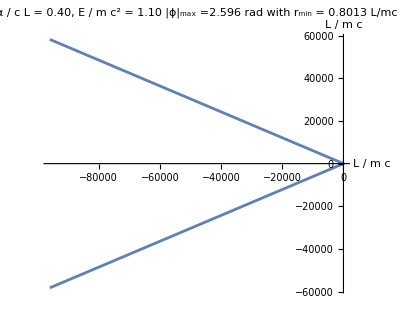

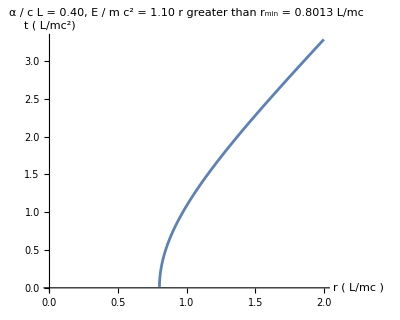

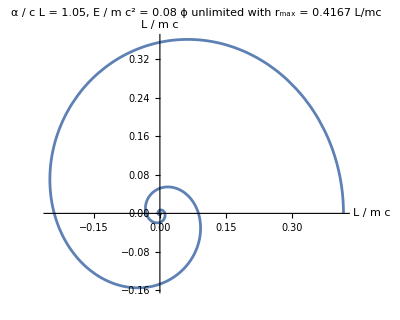

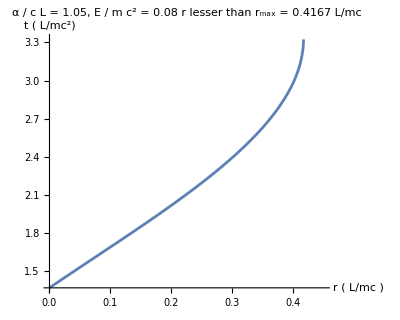

```mathematica
Clear["Global`*"]
PolarPlot[(α^2-1)/(√(-α β+√(α^2 β^2-(β^2-1)(α^2-1))Cosh[√(-1+α^2)ϕ]))/.{α->1.1,β->1.1},{ϕ,0.3826,8π},AxesLabel->{"L / m c","L / m c"},PlotLabel->Column[{Style["α / c L = 1.10, E / m c^2 = 1.10",12,FontFamily->"Times New Roman"],Style["|ϕ|_min = 0.3826 rad with r non-negative\n",12,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8
]
Plot[(β/(β^2-1)√((β^2-1)x^2+2α β x+α^2-1)-α/((β^2-1)^(3/2))ArcCosh[(α β+x(β^2-1))/(√(α^2 β^2-(β^2-1)(α^2-1)))])/.{α->1.1,β->1.1},{x,0,0.2},AxesLabel->{"r ( L/mc )","t ( L/mc^2)"},PlotLabel->Column[{Style["α / c L = 1.10, E / m c^2 = 1.10",12,FontFamily->"Times New Roman"],Style["r non-negative \n",12,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8
]
PolarPlot[(-α^2+1)/(α β+√(α^2 β^2-(β^2-1)(α^2-1))Cos[√(1-α^2)ϕ])/.{α->0.48,β->0.95},{ϕ,-8π,8π},AxesLabel->{"L / m c","L / m c"},PlotLabel->Column[{Style["α / c L = 0.48, E / m c^2 = 0.95",12,FontFamily->"Times New Roman"], Style["ϕ unlimited with r_min = 0.9379 L/mc and r_max = 8.416 L/mc\n",12,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8
]
Plot[(β/(β^2-1)√((β^2-1)x^2+2α β x+α^2-1)+α/((-β^2+1)^(3/2))ArcCos[(α β+x(β^2-1))/(√(α^2 β^2-(β^2-1)(α^2-1)))])/.{α->0.48,β->0.95},{x,0,8.5},AxesLabel->{"r ( L/mc )","t ( L/mc^2)"},PlotLabel->Column[{Style["α / c L = 0.48, E / m c^2 = 0.95",12,FontFamily->"Times New Roman"],Style["r limited between r_min = 0.9379 L/mc and r_max = 8.416 L/mc\n\n",12,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8,AxesOrigin->{0,0}
]
PolarPlot[(-α^2+1)/(1+√(1-((β^2-1)(α^2-1))/(α^2 β^2))Cos[√(1-α^2)ϕ])/.{α->0.4,β->1.1},{ϕ,-2.59618,2.59618},AxesLabel->{"L / m c","L / m c"},PlotLabel->Column[{Style["α / c L = 0.40, E / m c^2 = 1.10",12,FontFamily->"Times New Roman"],Style["|ϕ|_max =2.596 rad with r_min = 0.8013 L/mc \n",12,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8
]
Plot[(β/(β^2-1)√((β^2-1)x^2+2α β x+α^2-1)-α/((β^2-1)^(3/2))ArcCosh[(α β+x(β^2-1))/(√(α^2 β^2-(β^2-1)(α^2-1)))])/.{α->0.4,β->1.1},{x,0,2},AxesLabel->{"r ( L/mc )","t ( L/mc^2)"},PlotLabel->Column[{Style["α / c L = 0.40, E / m c^2 = 1.10",12,FontFamily->"Times New Roman"],Style["r greater than r_min = 0.8013 L/mc \n",12,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8
]
PolarPlot[(α^2-1)/(-α β+√(α^2 β^2-(β^2-1)(α^2-1))Cosh[√(-1+α^2)ϕ])/.{α->1.05,β->0.08},{ϕ,0,8π},AxesLabel->{"L / m c","L / m c"},PlotRange->All,PlotLabel->Column[{Style["α / c L = 1.05, E / m c^2 = 0.08",12,FontFamily->"Times New Roman"],Style["ϕ unlimited with r_max = 0.4167 L/mc\n",12,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8
]
Plot[(β/(β^2-1)√((β^2-1)x^2+2α β x+α^2-1)+α/((-β^2+1)^(3/2))ArcCos[(α β+x(β^2-1))/(√(α^2 β^2-(β^2-1)(α^2-1)))])/.{α->1.05,β->0.08},{x,0,0.45},AxesLabel->{"r ( L/mc )","t ( L/mc^2)"},PlotLabel->Column[{Style["α / c L = 1.05, E / m c^2 = 0.08",12,FontFamily->"Times New Roman"],Style["r lesser than r_max = 0.4167 L/mc\n",12,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8
]
```

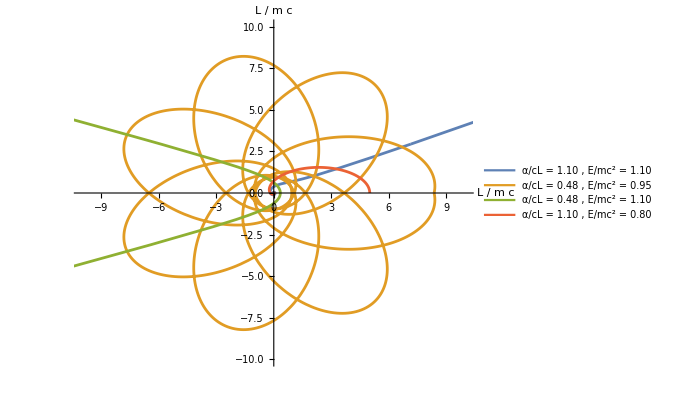

```mathematica
Clear["Global`*"];

(*---全局字体：所有文字都走 Times---*)
timesStyle={FontFamily->"Times New Roman"};

(*4 组参数*)
params={{α->1.1,β->1.1},{α->0.48,β->0.95},{α->0.48,β->1.1},{α->1.1,β->0.8}};

(*自动 legend 文本（从 params 自动识别 α、β）*)
labels=(StringTemplate["α/cL = `` , E/mc^2 = ``"]@@(NumberForm[#,{Infinity,2}]&/@({α,β}/. #)))&/@params;

(*不同颜色（自动配色），全部实线*)
colors=ColorData[97]/@Range[Length[params]];
styles=(Directive[#,Thick]&/@colors);

(*4 条 r(phi)，保持各自 phi 范围*)
rphiPlots={PolarPlot[((α^2-1)/Sqrt[-α β+Sqrt[α^2 β^2-(β^2-1) (α^2-1)] Cosh[Sqrt[-1+α^2] ϕ]])/. params[[1]],{ϕ,0.3826,8 π},PlotStyle->styles[[1]]],PolarPlot[((-α^2+1)/(α β+Sqrt[α^2 β^2-(β^2-1) (α^2-1)] Cos[Sqrt[1-α^2] ϕ]))/. params[[2]],{ϕ,-8 π,8 π},PlotStyle->styles[[2]]],PolarPlot[((-α^2+1)/(1+Sqrt[1-((β^2-1) (α^2-1))/(α^2 β^2)] Cos[Sqrt[1-α^2] ϕ]))/. params[[3]],{ϕ,-2.8,2.8},PlotStyle->styles[[3]]],PolarPlot[((α^2-1)/(-α β+Sqrt[α^2 β^2-(β^2-1) (α^2-1)] Cosh[Sqrt[-1+α^2] ϕ]))/. params[[4]],{ϕ,0,8 π},PlotStyle->styles[[4]]]};

(*合并+定区域+Times 字体+legend Times 字体*)
rphiAll=Legended[Show[rphiPlots,PlotRange->{{-10,10},{-10,10}},ImageSize->500,(*你要的固定区域*)AxesLabel->(Style[#,timesStyle]&/@{"L / m c","L / m c"}),AspectRatio->0.8,(*关键：把所有默认文字（ticks 等）也变成 Times*)BaseStyle->timesStyle,LabelStyle->timesStyle,TicksStyle->timesStyle],Placed[LineLegend[styles,(Style[#,timesStyle,FontSize->10]&/@labels),LabelStyle->timesStyle,LegendFunction->(Framed[#,FrameStyle->None,Background->None]&)],Right]];

rphiAll
```

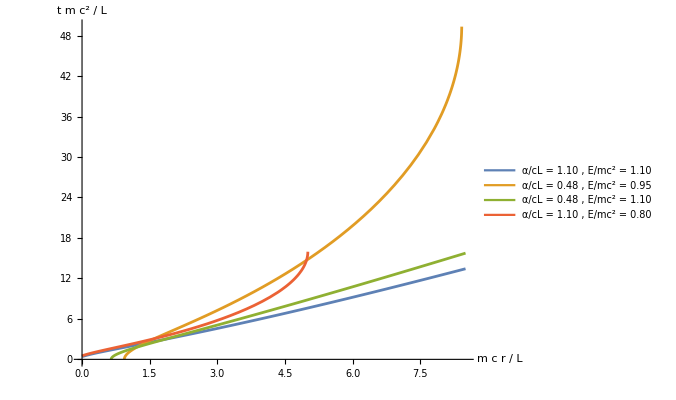

```mathematica
ClearAll[tPlots,tAll];

timesStyle={FontFamily->"Times New Roman"};

params={{α->1.1,β->1.1},{α->0.48,β->0.95},{α->0.48,β->1.1},{α->1.1,β->0.8}};

labels=(StringTemplate["α/cL = `` , E/\!\(\*SuperscriptBox[\(mc\), \(2\)]\) = ``"]@@(NumberForm[#,{Infinity,2}]&/@({α,β}/. #)))&/@params;

colors=ColorData[97]/@Range[Length[params]];
styles=Directive[#,Thick]&/@colors;

tPlots={Plot[((β/(β^2-1) Sqrt[(β^2-1) x^2+2 α β x+α^2-1]-α/(β^2-1)^(3/2) ArcCosh[(α β+x (β^2-1))/Sqrt[α^2 β^2-(β^2-1) (α^2-1)]])/. params[[1]]),{x,0,8.5},PlotStyle->styles[[1]],PlotLabel->None],Plot[((β/(β^2-1) Sqrt[(β^2-1) x^2+2 α β x+α^2-1]+α/(-β^2+1)^(3/2) ArcCos[(α β+x (β^2-1))/Sqrt[α^2 β^2-(β^2-1) (α^2-1)]])/. params[[2]]),{x,0,8.5},PlotStyle->styles[[2]],PlotLabel->None],Plot[((β/(β^2-1) Sqrt[(β^2-1) x^2+2 α β x+α^2-1]-α/(β^2-1)^(3/2) ArcCosh[(α β+x (β^2-1))/Sqrt[α^2 β^2-(β^2-1) (α^2-1)]])/. params[[3]]),{x,0,8.5},PlotStyle->styles[[3]],PlotLabel->None],Plot[((β/(β^2-1) Sqrt[(β^2-1) x^2+2 α β x+α^2-1]+α/(-β^2+1)^(3/2) ArcCos[(α β+x (β^2-1))/Sqrt[α^2 β^2-(β^2-1) (α^2-1)]])/. params[[4]]),{x,0,8.5},PlotStyle->styles[[4]],PlotLabel->None]};

tAll=Legended[Show[tPlots,PlotRange->All,ImageSize->500,AxesOrigin->{0,0},AxesLabel->(Style[#,timesStyle]&/@{"m c r / L","t m c^2 / L"}),AspectRatio->0.8,BaseStyle->timesStyle,LabelStyle->timesStyle,TicksStyle->timesStyle],Placed[LineLegend[styles,(Style[#,timesStyle,FontSize->10]&/@labels),LabelStyle->timesStyle,LegendFunction->(Framed[#,FrameStyle->None,Background->None]&)],Right]];

tAll
```

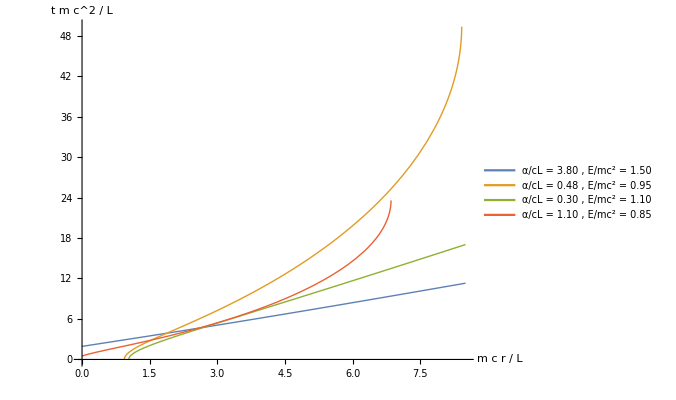
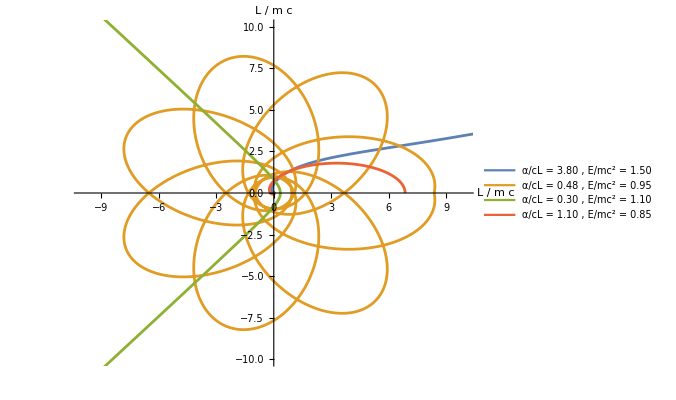

```mathematica
Clear["Global`*"];

(* =========全局字体=========*)
timesStyle={FontFamily->"Times New Roman"};

(* =========共用参数（你给的）=========*)
params={{α->3.8,β->1.5},{α->0.48,β->0.95},{α->0.3,β->1.1},{α->1.1,β->0.85}};

(* =========自动 legend 文本=========*)
labels=(StringTemplate["α/cL = `` , E/\!\(\*SuperscriptBox[\(mc\), \(2\)]\) = ``"]@@(NumberForm[#,{Infinity,2}]&/@({α,β}/. #)))&/@params;

(* =========统一配色（全实线）=========*)
colors=ColorData[97]/@Range[Length[params]];
styles=Directive[#,Thick]&/@colors;

(* =========================================================1) t(r) 合并（按你给的四条 Plot 原式，不改）=========================================================*)
tPlots={Plot[((β/(β^2-1) Sqrt[(β^2-1) x^2+2 α β x+α^2-1]-α/(β^2-1)^(3/2) ArcCosh[(α β+x (β^2-1))/Sqrt[α^2 β^2-(β^2-1) (α^2-1)]])/. params[[1]]),{x,0,8.5},PlotStyle->styles[[1]],PlotLabel->None],Plot[((β/(β^2-1) Sqrt[(β^2-1) x^2+2 α β x+α^2-1]+α/(-β^2+1)^(3/2) ArcCos[(α β+x (β^2-1))/Sqrt[α^2 β^2-(β^2-1) (α^2-1)]])/. params[[2]]),{x,0,8.5},PlotStyle->styles[[2]],PlotLabel->None],Plot[((β/(β^2-1) Sqrt[(β^2-1) x^2+2 α β x+α^2-1]-α/(β^2-1)^(3/2) ArcCosh[(α β+x (β^2-1))/Sqrt[α^2 β^2-(β^2-1) (α^2-1)]])/. params[[3]]),{x,0,8.5},PlotStyle->styles[[3]],PlotLabel->None],Plot[((β/(β^2-1) Sqrt[(β^2-1) x^2+2 α β x+α^2-1]+α/(-β^2+1)^(3/2) ArcCos[(α β+x (β^2-1))/Sqrt[α^2 β^2-(β^2-1) (α^2-1)]])/. params[[4]]),{x,0,8.5},PlotStyle->styles[[4]],PlotLabel->None]};

tAll=Legended[Show[tPlots,PlotRange->All,ImageSize->500,AxesOrigin->{0,0},AxesLabel->(Style[#,timesStyle]&/@{"m c r / L","t m c^2 / L"}),AspectRatio->0.8,BaseStyle->timesStyle,LabelStyle->timesStyle,TicksStyle->timesStyle],Placed[LineLegend[styles,(Style[#,timesStyle,FontSize->10]&/@labels),LabelStyle->timesStyle,LegendFunction->(Framed[#,FrameStyle->None,Background->None]&)],Right]];

(* =========================================================2) r(phi) 合并（按你给的四条 PolarPlot 原式，不改）=========================================================*)
rphiPlots={PolarPlot[((α^2-1)/Sqrt[-α β+Sqrt[α^2 β^2-(β^2-1) (α^2-1)] Cosh[Sqrt[-1+α^2] ϕ]])/. params[[1]],{ϕ,0.1,8 π},PlotStyle->styles[[1]],PlotLabel->None],PolarPlot[((-α^2+1)/(α β+Sqrt[α^2 β^2-(β^2-1) (α^2-1)] Cos[Sqrt[1-α^2] ϕ]))/. params[[2]],{ϕ,-8 π,8 π},PlotStyle->styles[[2]],PlotLabel->None],PolarPlot[((-α^2+1)/(1+Sqrt[1-((β^2-1) (α^2-1))/(α^2 β^2)] Cos[Sqrt[1-α^2] ϕ]))/. params[[3]],{ϕ,-2.3,2.3},PlotStyle->styles[[3]],PlotLabel->None],PolarPlot[((α^2-1)/(-α β+Sqrt[α^2 β^2-(β^2-1) (α^2-1)] Cosh[Sqrt[-1+α^2] ϕ]))/. params[[4]],{ϕ,0,8 π},PlotStyle->styles[[4]],PlotLabel->None
]
};

rphiAll=Legended[Show[rphiPlots,PlotRange->{{-10,10},{-10,10}},ImageSize->500,AxesLabel->(Style[#,timesStyle]&/@{"L / m c","L / m c"}),AspectRatio->0.8,BaseStyle->timesStyle,LabelStyle->timesStyle,TicksStyle->timesStyle],Placed[LineLegend[styles,(Style[#,timesStyle,FontSize->10]&/@labels),LabelStyle->timesStyle,LegendFunction->(Framed[#,FrameStyle->None,Background->None]&)],Right]];

(* =========================================================3) 导出 PNG（在你本机 Mathematica 运行）=========================================================*)

outDir="E:\\移动云盘同步盘\\Desktop\\笔记本\\已转换笔记\\一次反比势场中的运动\\";
If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];

Export[FileNameJoin[{outDir,"t_all.png"}],tAll,ImageResolution->300];
Export[FileNameJoin[{outDir,"rphi_all.png"}],rphiAll,ImageResolution->300];

(*显示图*)
{tAll,rphiAll}
```